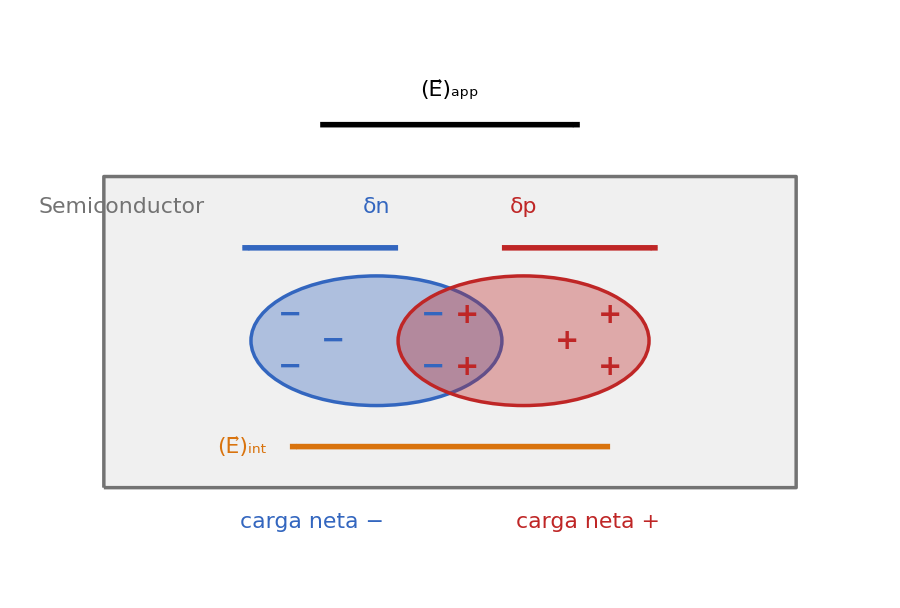

```mathematica
diagramaAmbipolar = Module[
  {fs, cAzul, cRojo, cNar, cGris, ins, tx, signo, flecha,
   rx, ry, yc, xe, xh, xm},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;   (* tamaño de fuente único para todo el gráfico *)
  cAzul = RGBColor[0.20, 0.40, 0.75];  cRojo = RGBColor[0.75, 0.15, 0.15];
  cNar  = RGBColor[0.85, 0.45, 0.05];  cGris = GrayLevel[0.45];

  (* ---------- Geometría ---------- *)
  {rx, ry} = {2.9, 1.5};     (* semiejes de las nubes de exceso *)
  yc = 3.4;                  (* altura central de las nubes *)
  {xe, xh} = {6.3, 9.7};     (* centros: electrones a la izquierda, huecos a la derecha *)
  xm = (xe + xh)/2;          (* centro de la región excitada *)

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  tx[expr_, pos_, al_, col_: Black] := Text[Style[expr, fs, col], pos, al];
  signo[s_, pos_, col_] := Text[Style[s, Round[1.3 fs], Bold, col], pos];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.03], Arrow[{p1, p2}]};

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* semiconductor *)
    {GrayLevel[0.94], EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{0, 0}, {16, 7.2}]},
    tx["Semiconductor", {0.4, 6.5}, {-1, 0}, cGris],

    (* nubes de exceso: δn (electrones) y δp (huecos) *)
    {Opacity[0.35, cAzul], EdgeForm[{AbsoluteThickness[2.5], Opacity[1, cAzul]}],
     Disk[{xe, yc}, {rx, ry}]},
    {Opacity[0.35, cRojo], EdgeForm[{AbsoluteThickness[2.5], Opacity[1, cRojo]}],
     Disk[{xh, yc}, {rx, ry}]},

    (* exceso neto de electrones (izquierda) y de huecos (derecha) *)
    signo["−", {xe - 2.0, yc + 0.6}, cAzul],
    signo["−", {xe - 2.0, yc - 0.6}, cAzul],
    signo["−", {xe - 1.0, yc}, cAzul],
    signo["+", {xh + 2.0, yc + 0.6}, cRojo],
    signo["+", {xh + 2.0, yc - 0.6}, cRojo],
    signo["+", {xh + 1.0, yc}, cRojo],

    (* zona solapada: pares electrón-hueco, carga neta nula *)
    Table[
     {signo["−", {xm - 0.4, yy}, cAzul],
      signo["+", {xm + 0.4, yy}, cRojo]},
     {yy, {yc + 0.6, yc - 0.6}}],

    (* tendencia a la separación por el campo aplicado *)
    flecha[{xe + 0.5, 5.55}, {xe - 3.1, 5.55}, cAzul],
    flecha[{xh - 0.5, 5.55}, {xh + 3.1, 5.55}, cRojo],
    ins[Row[{"δ", Style["n", Italic]}], {xe, 6.5}, cAzul],
    ins[Row[{"δ", Style["p", Italic]}], {xh, 6.5}, cRojo],

    (* campo interno: de + a −, opuesto a la separación *)
    flecha[{xh + 2.0, 0.95}, {xe - 2.0, 0.95}, cNar],
    ins[Row[{Subscript[OverVector["E"], "int"]}], {xe - 3.1, 0.95}, cNar],

    (* carga neta en cada extremo *)
    tx["carga neta −", {xe - 1.5, -0.8}, {0, 0}, cAzul],
    tx["carga neta +", {xh + 1.5, -0.8}, {0, 0}, cRojo],

    (* campo eléctrico aplicado *)
    flecha[{xm - 3.0, 8.4}, {xm + 3.0, 8.4}, Black],
    ins[Row[{Subscript[OverVector["E"], "app"]}], {xm, 9.2}]
   },
   ImageSize -> 900,
   PlotRange -> {{-0.5, 16.5}, {-1.5, 10.0}},
   PlotRangePadding -> None,
   AspectRatio -> 11.5/17,
   Background -> White]
];
diagramaAmbipolar
```